The purpose of this project was to generate a playable game of PacMan with a street map. I used Open Street Map to access geographic data for a city and built a movement system around that data. I then implemented movement patterns for ghosts using a similar structure to PacMan, which ultimately allowed PacMan and the ghosts to traverse roads and respond to player clicks. Finally, I added extra game features, including power pellets and a scoring system, to construct a finalized version of my game.

## Introduction

The game PacMan was made in 1980 by a Japanese arcade game manufacturer called Namco limited. It soon spread to arcades throughout the world inspiring popular songs, television series, and many replications of the game across multiple platforms. PacMan's popularity has made it into a household name with 94% of Americans recognizing the game and the character in 2008. Today, PacMan can be found on many arcade machines and a simple internet search can let one play it from their computer. With this project, I have made yet another rendition of this popular game but with a twist: the game is now played with a street map.

## Open Street Map

Open Street Map (OSM) is a public database with information about streets collected through volunteers, aerial data, and other sources. This makes it a popular tool for individuals, companies, and government organizations.

### Importing data

There are many ways to access data from Open Street Map such as downloading the XML file containing the data. This was the option I utilized first, as the Wolfram Resource Function OSMImport supported XML files and converted them into a more flexible association. This meant I could select a region, download it, and quickly have it on hand with an OSM import.

Importing data from a file that was put on the cloud:

```mathematica
CloudGet["https://www.wolframcloud.com/obj/sameeragarwal007/OSMFile"];
```

Another option is by taking the minimum and maximum latitude and longitude coordinates to find the bounding region and input it into the OSM import. This turned out to be an easier way to access data as I only had to enter a set of coordinates with the option to quickly select any region and it would download the data into AppData. I started using this method in later stages of my project.

Importing data from a region:

```mathematica
openStreetMapRegion=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.68272,40.69689},{-73.8668,-73.85069}}]];
```

Example of data present in Open Street Map:

```mathematica
openStreetMapRegionPart=openStreetMapRegion[[1]][[10]]
```

The final way to access data from Open Street Map is through an API like Overpass API. Overpass offers an advanced Query language which allows users to gain larger amounts of data than normal imports and request specific data rather than all of it. This was a complicated method that was unnecessary to my goal of constructing a small scale game of PacMan.

### Visualization

After importing the data, I used GeoGraphics to visualize the data on a map and I could use tags that were present in the data set to isolate and visualize specific features of the map I wanted such as highways, residential roads, and traffic signals.

Visualizing OSM data on a map with GeoGraphics using MatchQ:

```mathematica
GeoGraphics[
	Values[
		Line[
			Values[
				openStreetMapRegion[["Nodes",#Nodes,"Position"]]]]&/@
					Select[
					openStreetMapRegion["Ways"],MatchQ[
					#[["Tags","highway"]],
						"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]]
```

## Movement of PacMan

In traditional PacMan games, PacMan moves along a grid with walls allowing for complex maneuvers. This grid-style map allows joysticks and arrow keys to be easy methods of obtaining user input.

Simple Grid code for movement of PacMan with arrow keys:

```mathematica
DynamicModule[{pos={0,0}},EventHandler[Graphics[{RGBColor["Gold"],Dynamic[Disk[pos,1]]},
PlotRange->{{-15,15},{-15,15}},Frame->True,FrameTicks->True,GridLines->{Range[-15,15,2],Range[-15,15,2]}],
{"UpArrowKeyDown":>If[pos[[2]]<14,(pos+={0,2}),None],"DownArrowKeyDown":>If[pos[[2]]>-14,(pos-={0,2}),None],
"LeftArrowKeyDown":>If[pos[[1]]>-14,(pos-={2,0}),None],"RightArrowKeyDown":>If[pos[[1]]<14,(pos+={2,0}),None]}]]
```

-Graphics-

However, as my map is in a different form from the typical grid, it required a new type of movement. Deep analysis of the OSM data let me figure out how each street was made up of a group of nodes. This means that if I could create a function that could move through a list of points, it would move from node to node, therefore simulating movement across my lined map.

Extracting lines without graphing them:

```mathematica
generateLines[openStreetMapData_]:=Values[Line[
	Values[
		openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@
		Select[openStreetMapData["Ways"],
		MatchQ[#[["Tags","highway"]],
		"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
		GeoPosition[{a_,b_}]:> {b,a}
```

Visualization of lines:

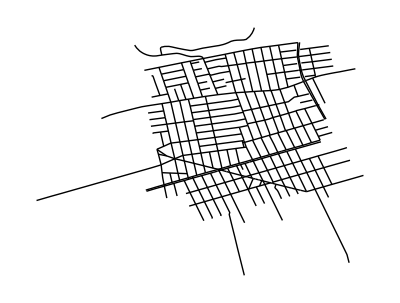

```mathematica
Graphics[line]
```

I started by working with diagonal movement by using vectors. The Normalize function helped me to update the position of a dynamic object in a dynamic module every frame with the vector.

Moving PacMan from one random point to another random point using vectors:

```mathematica
vectorMovement[point_]:=
DynamicModule[
			{pos={-73.859,40.685},movement=False},
			EventHandler[
				Graphics[{line=generateLines[openStreetMapRegion],
					Dynamic[Disk[pos+=
					If[
					EuclideanDistance[point,pos]>0.0001&&movement==True,
					Normalize[point-pos]*0.00001,0],0.0003]]},
					PlotRange->{{-73.8668,-73.85069},{40.68272,40.69689}}],
					{"MouseClicked":>(movement=True)}]]
```

```mathematica
vectorMovement[{-73.864706,40.687562}]
```

-Graphics-

I then edited this dynamic module to allow a list of points to be inserted and PacMan would bounce between these points.

Continuous movement between points(traffic signals) in a list:

```mathematica
intersections=Values[Values/@
Select[openStreetMapRegion["Nodes"],MatchQ[#[["Tags","highway"]],"traffic_signals"]&]]/.
{GeoPosition[{a_,b_}],<|___|>}:> {b,a};

listMovement[points_]:=DynamicModule[
		{pos={-73.859,40.685},movement=False,current=1,line=generateLines[openStreetMapRegion]},
		EventHandler[
			Graphics[{line,Dynamic[
			Disk[pos+=Which[
			EuclideanDistance[points[[current]],pos]>0.0001&&movement==True,
			Normalize[points[[current]]-pos]*0.00001,
			EuclideanDistance[points[[current]],pos]<0.0001&&current<Length[points],
			current+=1;0,True,0],0.0003]]},
			PlotRange->{{-73.8768,-73.84069},{40.67272,40.70689}}
		],{
"MouseClicked":>(movement=True;)}]]
```

```mathematica
listMovement[intersections]
```

-Graphics-

### Trajectory and navigation

To do navigation I experimented with many methods and realized the most effective one would be through clicking. The player would click where they want PacMan to go and it would navigate to that area. To begin this, I used my single point navigation, found the nearest node to the mouse click and navigated there.

List of nodes made by retrieving points off of the OSM lines:

```mathematica
generateNodes[osm4_,area_]:=
DeleteCases[Reverse[#,2]&/@
(Values[
	Values[
		osm4[["Nodes",#Nodes,"Position"]]]
		&/@Select[
			osm4["Ways"],
		MatchQ[#[["Tags","highway"]],
		"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]
		/.GeoPosition[{a_,b_}]:> {a,b}),{lon_,lat_}/;!(Between[lat,area[[1]]])||!(Between[lon,area[[2]]]),{-2}]
```

PacMan navigating to the node closest to the mouse position:

```mathematica
mouseNavigation[]:=DynamicModule[
	{pos={-73.859,40.685},movement=False,p={0,0},line=generateLines[openStreetMapRegion],
	node=generateNodes[openStreetMapRegion,{{40.68272,40.69689},{-73.8668,-73.85069}}]},
	EventHandler[
		Graphics[{line,
		Dynamic[Disk[pos+=
		If[EuclideanDistance[p,pos]>0.0001&&movement==True,
		Normalize[p-pos]*0.00001,0],0.0003]]},
		PlotRange->{{-73.8768,-73.84569},{40.67272,40.70}}],
		{
		"MouseClicked":>(movement=True;
		p=First[Nearest[Flatten[node,1],MousePosition["Graphics"],1]])
		}
	]
]
```

```mathematica
mouseNavigation[]
```

-Graphics-

From here, I remembered that I had to go from node to node to move across the lines. This inspired me to make a graph by combining my nodes from earlier into edges. The goal of using a graph was to apply the FindShortestPath to navigate between nodes.

Generating a graph:

```mathematica
generateGraph[nodes_]:=Graph[Flatten[UndirectedEdge@@@Partition[#,2,1]&/@nodes,1]];
```

```mathematica
graphOfNodes=generateGraph[node];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[node,1].

Using FindShortestPath to make a list of nodes along a path highlighting that path:

```mathematica
path=FindShortestPath[graphOfNodes,RandomChoice[RandomChoice[node]],Flatten[Nearest[Flatten[node,1],{-73.842027,40.695}],1]];
HighlightGraph[graphOfNodes,path]
```

This graph would allow me to find the shortest path from node to node and move the PacMan through the nodes using the previous iteration of the movement function involving a list of points.

Combined movement function:

```mathematica
movement[]:=DynamicModule[
	{pos={-73.8590766,40.6868511},movement=False,dest={{0,0},{0,1}},line=generateLines[openStreetMapRegion],
	node=generateNodes[openStreetMapRegion,{{40.68272,40.69689},{-73.8668,-73.85069}}]},
	EventHandler[Graphics[{line,Dynamic[Disk[pos+=
		Which[EuclideanDistance[First[dest],pos]>0.00001&&movement==True,
		Normalize[First[dest]-pos]*0.00001,
		EuclideanDistance[First[dest],pos]<0.00001&&Length[dest]>=1,
		pos=First[dest];
		Which[Length[dest]>1,dest=Rest[dest],(Length[dest]==1||Length@dest==1),movement=False];
		0,
		True,
		0],
			0.0003
		]]
		},
		PlotRange->{{-73.850,-73.868},{40.679,40.698}}
		
		],
		{
		"MouseClicked":>
		(movement=True;
		dest=Rest[FindShortestPath[graphOfNodes,pos,Flatten[Nearest[Flatten[node,1],
		MousePosition["Graphics"],1]]]]
		)
	}
	]
]
```

```mathematica
movement[]
```

-Graphics-

#### Compiling movement

Compiling these iterations of movement allowed me to produce a finalized movement function with a few minor changes. One such change was making the FindShortestPath into a helper function called navigation to make the code easier to digest.

Helper function to find the shortest path between points:

```mathematica
navigation[graph_,point1_,point2_,nodes_]:=
Rest[FindShortestPath[graph,point1,Flatten[Nearest[Flatten[nodes,1],point2,1]]]];
```

The previous movement function above had a flaw where it would cause errors when the mouse was clicked before PacMan made it to the end of his path. In order to fix this, I made a DuringPath variable to determine whether PacMan was still on his route or he had reached his destination. Upon a mouse click, if DuringPath was true, I would run a different navigation function called rerouting. The rerouting function uses FindShortestPath but assumes neither point is a node; it navigates to the node nearest to the first point, and from there it navigates to the node nearest to the second point.

Navigation function between two non-node points:

```mathematica
rerouting[graph_,point1_,point2_,nodes_]:=
FindShortestPath[graph,Flatten[Nearest[Flatten[nodes,1],point1,1]],
Flatten[Nearest[Flatten[nodes,1],point2,1]]];
```

These changes were used to make the final version of the movement function for PacMan.

Final version of movement for PacMan:

```mathematica
movementFinal[]:=DynamicModule[
	{pos={-73.8592119,40.6903749},movement=False,dest={{0,0},{0,1}},duringPath=False,line=generateLines[openStreetMapRegion],
	node=generateNodes[openStreetMapRegion,{{40.68272,40.69689},{-73.8668,-73.85069}}]},
	EventHandler[
Graphics[
				{
					line,RGBColor["Gold"],
					Dynamic[Disk[
						pos+=Which[
							movement==True&&EuclideanDistance[First[dest],pos]>0.00001,
								Normalize[First[dest]-pos]*0.00001,
							EuclideanDistance[First[dest],pos]<0.00001&&Length[dest]>0,
								pos=First[dest];
								Which[Length[dest]>1,dest=Rest[dest],
								(Length[dest]==1||Length@dest==1),
								movement=False;duringPath=False];
								0,
							True,
								0
						],
						0.0004
					]]
				},
				PlotRange->{{-73.850,-73.868},{40.679,40.698}}
				
			],
		{
			"MouseClicked":>(If[duringPath==True,
			dest=rerouting[graphOfNodes,pos,MousePosition["Graphics"],node],
			dest=navigation[graphOfNodes,pos,MousePosition["Graphics"],node]];
				movement=True;duringPath=True	
			)
		}
	]
]
```

```mathematica
movementFinal[]
```

-Graphics-

I continued to add features onto this function to make the final version of my game.

## Movement of Ghosts

When developing the ghosts into the game, I added them directly on to the movement function as they required interaction with PacMan and specific variables that couldn’t be achieved through helper functions. This means that code below will not run as it’s a part of a larger piece of code.

### Individual movement

In PacMan, there are 4 different ghosts: Blinky, Pinky, Inky, and Clyde which are better known as the red, pink, blue, and orange ghosts. As they attempt to track down PacMan, they use different movement patterns in order to corner the player.

Blinky is the chaser and they follow PacMan around directly. However, they can get confused sometimes and has partially erratic movements. To imitate this, whenever PacMan crossed a node, Blinky would calculate the shortest path from its current location to that node and move in that direction. This allowed Blinky to chase PacMan but also experience some confusion.

Blinky’s destination calculation:

```mathematica
redDest=rerouting[nodeGraph,redpos,pacmanPos,nodes];
```

Pinky is the ambusher and they navigate 2 - 4 tiles ahead of Pac Man to ambush him. They are more strategic and have a higher chance of catching PacMan. To create Pinky, whenever PacMan’s destination was set by the click of a mouse, Pinky would navigate to PacMan’s final destination— where the mouse was clicked. Once Pinky got to their destination, they would navigate towards PacMan to catch him.

Pinky’s destination calculation:

```mathematica
pinkDest=rerouting[nodeGraph,pinkpos,Last[dest],nodes]
```

Inky is a more unusual ghost as they operate off the locations of both PacMan and Blinky. They use Blinky’s distance from PacMan as a multiplier to determine their desired destination. When observing Inky’s movement during a game, I realized that their movement patterns caused it to frequently “Double Up” with another ghost for periods of time.

Unfortunately, I could not implement Inky’s normal movement due to more limited data so I decided to make a new system. This system would have an element of randomness as Inky would navigate to a node near PacMan’s current destination. This meant it had the possibility of doubling up with Pinky or Blinky.

Inky’s destination calculation:

```mathematica
blueDest=rerouting[nodeGraph,bluepos,RandomChoice[VertexList[NeighborhoodGraph[nodeGraph,Last[dest]]]],nodes]
```

Clyde is the “stupid” ghost who runs away to random locations when they are near PacMan. I implemented this by navigating Clyde to random nodes.

Clyde’s destination calculation:

```mathematica
orangeDest=navigation[nodeGraph,orangepos,RandomChoice[Flatten[nodes,1]],nodes];
```

Below is one full block for a ghost’s movement which contains many similar elements to PacMan’s navigation as it navigates between nodes in a similar way.

Full Block of code for a ghost:

```mathematica
RGBColor[Orange],
Dynamic[Disk[orangepos+=Which[
				ghostMovement==True&&EuclideanDistance[orangepos,First[orangeDest]]>0.00001 ,
								Normalize[First[orangeDest]-orangepos]*0.00001,
							EuclideanDistance[orangepos,First[orangeDest]]<0.00001,
								orangepos=First[orangeDest];
								Which[Length[orangeDest]>1,orangeDest=Rest[orangeDest],Length[orangeDest]==1,orangeDest=navigation[nodeGraph,orangepos,RandomChoice[Flatten[nodes,1]],nodes]];
								0,
							True,
								0
						],0.0005
]];
```

### Interactions with PacMan

The next thing to consider for ghosts was their interactions with PacMan. Whenever they hit PacMan, he loses a life - if he has any - and all positions and destinations are reset along and starting variables.

Reset code if PacMan was hit:

```mathematica
If[EuclideanDistance[orangepos,pos]<0.00001,lives--;
movement=False;ghostMovement=False;{pos,pinkpos,orangepos,bluepos,redpos}={ogPac,ogPink,ogOrange,ogBlue,ogRed};speed=1;redDest=navigationworse[nodeGraph,redpos,pos,nodes];
pinkDest=navigationworse[nodeGraph,pinkpos,pos,nodes];
orangeDest=navigationworse[nodeGraph,orangepos,pos,nodes];
blueDest=navigationworse[nodeGraph,bluepos,pos,nodes]];
```

Due to high quantities of variables being reset, I repeated this code for each ghost instead of creating a function.

## Additional Game Features

### Scoring system

To use all of these scoring methods I created a variable called score which handles standard pellets and Power Pellets.

#### Pellets

To generate pellets into my game I placed them on nodes, to ensure that there weren't too many pellets, I only chose 2/3rd of the nodes as pellets with a generatePellets function

Generates pellets using nodes:

```mathematica
generatePellets[nodes_]:=RandomChoice[Flatten[nodes,1],Length[nodes]/1.5]
```

These were then placed down as small disks at their locations.

Places pellets down:

```mathematica
Dynamic[Disk[#,0.00006]&/@pellets]
```

Whenever PacMan reached a node, I checked if that node contained a pellet. If it did, I updated the score and removed that pellet from the list of pellets.

Checks if PacMan is on a pellet and updates score accordingly:

```mathematica
If [MemberQ[pellets,First[dest]]==True,score=score+10;pellets=DeleteCases[pellets,First[dest]],None];
```

#### Eating ghosts

In PacMan, whenever he eats a Power Pellet, he gains the ability to consume the ghosts and gain points. To implement the powerPellets I took a random 7 pellets and made them powerPellets

Making seven Power Pellets:

```mathematica
powerPellets=RandomChoice[pellets,7];
```

Displays Power Pellets:

```mathematica
Dynamic[Disk[#,0.00008]&/@powerPellets]
```

Power mode if PacMan passes over a Power Pellet:

```mathematica
If[MemberQ[powerPellets,First[dest]]==True,powerMode=10;powerPellets=DeleteCases[powerPellets,First[dest]],None];
```

Function to check which ghost PacMan hit:

```mathematica
whichGhost[pos_,pos2_,pos3_,pos4_,pos5_]:=Flatten[Nearest[{pos2,pos3,pos4,pos5},pos,1],1]
```

Checks if PacMan hit a ghost and uses the previous function to find out which ghost and resets the ghosts position and destination. The player gets a score of 100 multiplied by the current multiplier and the multiplier is increased.

Code to check for PacMan and ghost interaction:

```mathematica
If[powerMode>0&&(EuclideanDistance[pos,redpos]<0.00001||EuclideanDistance[pos,bluepos]<0.00001||EuclideanDistance[pos,pinkpos]<0.00001||EuclideanDistance[pos,orangepos]<0.00001),Which[whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==redpos,redpos=ogRed;redDest=rerouting[nodeGraph,redpos,pos,nodes],whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==bluepos,bluepos=ogBlue;blueDest=rerouting[nodeGraph,bluepos,pos,nodes],whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==orangepos,orangepos=ogOrange;orangeDest=rerouting[nodeGraph,orangepos,pos,nodes],whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==pinkpos,pinkpos=ogPink;pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes]];score+=100*multiplier;multiplier+=1,None]
```

Over time, Power mode becomes less so it eventually runs out. I implemented this by subtracting 0.5 from it every time PacMan hits a node.

Power Mode "decaying”:

```mathematica
If[powerMode>0,If[powerMode>0.5,powerMode-=0.5,powerMode-=0.5;multiplier=1],None];
```

#### Display

To show the player their current score and lives I used insets to display text at a location.

Joins the score and lives to strings to inset them:

```mathematica
RGBColor[Red],Dynamic[Inset["Score: "<>ToString[score],{Right,Top},{Right,Top}]],Dynamic[Inset["Lives: "<>ToString[lives],{Left,Top},{Left,Top}]]
```

### Win and lose conditions

For either condition I added a boolean named round over whenever either a lose or win condition is met.

For lose conditions I added a part in the interactions between ghosts and PacMan that checks how many lives PacMan has left

Handling roundOver:

```mathematica
If[lives>1,lives--;(*rest of reset code*),lives--;roundOver=True]
```

To construct win conditions, after PacMan hits a node, it checks if there are any pellets left.

Checks if there are pellets:

```mathematica
If[Length[pellets]==0,roundOver=True,None];
```

## Final Game

All of the code was combined to create the final function. This contains every aspect of the game I developed and iterated on. At the bottom, I added a couple of locations with their bounding areas but this code can be run on any correctly sized region.

Final game code

```mathematica
level[area_]:=DynamicModule[
	{pos,ogPac,movement=False,dest={{0,0},{0,1}},duringPath=False,powerMode=0,multiplier=1,pellets,score=0,
	ghostMovement=False,roundOver=False,
	osm=ResourceFunction["OSMImport"][GeoBoundsRegion[area]],nodes,
	nodeGraph,
	pacImage=-Graphics-,redImage=-Graphics-,blueImage=-Graphics-,orangeImage=-Graphics-,pinkImage=-Graphics-,
redpos,redDest,ogRed,
pinkpos,pinkDest,ogPink,
orangepos,orangeDest,ogOrange,
bluepos,blueDest,ogBlue,
lines,speed=1,lives=3,powerPellets},
nodes=generateNodes[osm,area];
lines=generateLines[osm];
pellets=generatePellets[nodes];
powerPellets=RandomChoice[pellets,7];
nodeGraph=generateGraph[nodes];
pos=RandomChoice[RandomChoice[nodes]];
ogPac=pos;
redpos=RandomChoice[RandomChoice[nodes]];
ogRed=redpos;
pinkpos=RandomChoice[RandomChoice[nodes]];
ogPink=pinkpos;
orangepos=RandomChoice[RandomChoice[nodes]];
ogOrange=orangepos;
bluepos=RandomChoice[RandomChoice[nodes]];
ogBlue=bluepos;
redDest=rerouting[nodeGraph,redpos,pos,nodes];
pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes];
orangeDest=rerouting[nodeGraph,orangepos,pos,nodes];
blueDest=rerouting[nodeGraph,bluepos,pos,nodes];

EventHandler[
			(*Geo*)Graphics[
				{
		If[roundOver===True,Inset["Game Over",{Right,Top},{Right,Top}];
		movement=False;ghostMovement=False,Inset["Game in play",{Right,Bottom},{Right,Bottom}]],
					RGBColor[Red],
					Dynamic[Inset["Score: "<>ToString[score],{Right,Top},{Right,Top}]],
					Dynamic[Inset["Lives: "<>ToString[lives],{Left,Top},{Left,Top}]],
					RGBColor["Orange"],
Dynamic[Disk[#,0.00006]&/@pellets],RGBColor[Black],lines,
RGBColor[Red],
Dynamic[Disk[#,0.00008]&/@powerPellets],
					Dynamic[Inset[pacImage,
						pos+=If[roundOver==False,
						Which[powerMode>0&&(EuclideanDistance[pos,redpos]<0.00001||EuclideanDistance[pos,bluepos]<0.00001||
						EuclideanDistance[pos,pinkpos]<0.00001||EuclideanDistance[pos,orangepos]<0.00001),
						Which[whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==redpos,redpos=ogRed;
						redDest=rerouting[nodeGraph,redpos,pos,nodes],
						whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==bluepos,bluepos=ogBlue;
						blueDest=rerouting[nodeGraph,bluepos,pos,nodes],
						whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==orangepos,
						orangepos=ogOrange;orangeDest=rerouting[nodeGraph,orangepos,pos,nodes],
						whichGhost[pos,redpos,orangepos,pinkpos,bluepos]==pinkpos,pinkpos=ogPink;
						pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes]];score+=100*multiplier;multiplier+=1;0,
							movement==True&&EuclideanDistance[First[dest],pos]>0.00001,
								Normalize[First[dest]-pos]*0.000015,
							EuclideanDistance[First[dest],pos]<0.00001&&Length[dest]>0,
								If[MemberQ[pellets,First[dest]]==True,score=score+10;
								pellets=DeleteCases[pellets,First[dest]],None];
								If[Length[pellets]==0,roundOver=True,None];
								If[MemberQ[powerPellets,First[dest]]==True,powerMode=10;
								powerPellets=DeleteCases[powerPellets,First[dest]],None];
								If[powerMode>0,If[powerMode>0.5,powerMode-=0.5,powerMode-=0.5;multiplier=1],None];
								pos=First[dest];redDest=rerouting[nodeGraph,redpos,pos,nodes];
									Which[Length[dest]>1,dest=Rest[dest],Length[dest]===1,movement=False;
									duringPath=False;redDest=rerouting[nodeGraph,redpos,pos,nodes]];
								0,
							True,
								0
						],0],
					 Automatic,
						If[powerMode>0,0.001,0.0005]
					]],
			RGBColor[Red],Dynamic[Inset[redImage,
			redpos+=If[roundOver==False,Which[powerMode==0&&EuclideanDistance[redpos,pos]<0.00001,
			If[lives>1,lives--;movement=False;ghostMovement=False;
			{pos,pinkpos,orangepos,bluepos,redpos}={ogPac,ogPink,ogOrange,ogBlue,ogRed};
			speed=1;redDest=rerouting[nodeGraph,redpos,pos,nodes];
		pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes];
		orangeDest=rerouting[nodeGraph,orangepos,pos,nodes];
		blueDest=rerouting[nodeGraph,bluepos,pos,nodes],lives--;roundOver=True];0,
							ghostMovement==True&&EuclideanDistance[redpos,First[redDest]]>0.00001 ,
								Normalize[First[redDest]-redpos]*0.000012,
							EuclideanDistance[redpos,First[redDest]]<0.00001,
								redpos=First[redDest];
								Which[Length[redDest]>1,redDest=Rest[redDest],Length[redDest]===1,
								redDest=rerouting[nodeGraph,redpos,pos,nodes]];
								0,
							True,
								0
						],0],Automatic,0.0005
			]],
				RGBColor[Pink],Dynamic[Inset[pinkImage,
			pinkpos+=If[roundOver==False,Which[powerMode==0&&EuclideanDistance[pinkpos,pos]<0.00001,
			If[lives>1,lives--;movement=False;ghostMovement=False;
			{pos,pinkpos,orangepos,bluepos,redpos}={ogPac,ogPink,ogOrange,ogBlue,ogRed};
			speed=1;redDest=rerouting[nodeGraph,redpos,pos,nodes];
			pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes];
			orangeDest=rerouting[nodeGraph,orangepos,pos,nodes];
			blueDest=rerouting[nodeGraph,bluepos,pos,nodes],lives--;roundOver=True];0,
							ghostMovement==True&&EuclideanDistance[pinkpos,First[pinkDest]]>0.00001 ,
								Normalize[First[pinkDest]-pinkpos]*0.00001,
							EuclideanDistance[pinkpos,First[pinkDest]]<0.00001,
								pinkpos=First[pinkDest];
								Which[Length[pinkDest]>1,pinkDest=Rest[pinkDest],
								Length[pinkDest===1]||Length[pinkDest<1],pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes]];
								0,
							True,
								0
						],0],Automatic,0.0005
			]],
		RGBColor[Orange],Dynamic[Inset[orangeImage,
			orangepos+=If[roundOver==False,Which[powerMode==0&&EuclideanDistance[orangepos,pos]<0.00001,
			If[lives>1,lives--;movement=False;ghostMovement=False;
			{pos,pinkpos,orangepos,bluepos,redpos}={ogPac,ogPink,ogOrange,ogBlue,ogRed};speed=1;
			redDest=rerouting[nodeGraph,redpos,pos,nodes];
pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes];
orangeDest=rerouting[nodeGraph,orangepos,pos,nodes];
blueDest=rerouting[nodeGraph,bluepos,pos,nodes],lives--;roundOver=True];0,
							ghostMovement==True&&EuclideanDistance[orangepos,First[orangeDest]]>0.00001 ,
								Normalize[First[orangeDest]-orangepos]*0.00001,
							EuclideanDistance[orangepos,First[orangeDest]]<0.00001,
								orangepos=First[orangeDest];
								Which[Length[orangeDest]>1,orangeDest=Rest[orangeDest],
								Length[orangeDest]===1,
								orangeDest=navigation[nodeGraph,orangepos,RandomChoice[Flatten[nodes,1]],nodes]];
								0,
							True,
								0
						],0],Automatic,0.0005
			]],
	RGBColor[Blue],Dynamic[Inset[blueImage,
			bluepos+=If[roundOver==False,Which[powerMode==0&&EuclideanDistance[bluepos,pos]<0.00001,
			If[lives>1,lives--;movement=False;ghostMovement=False;
			{pos,pinkpos,orangepos,bluepos,redpos}={ogPac,ogPink,ogOrange,ogBlue,ogRed};
			speed=1;redDest=rerouting[nodeGraph,redpos,pos,nodes];
pinkDest=rerouting[nodeGraph,pinkpos,pos,nodes];
orangeDest=rerouting[nodeGraph,orangepos,pos,nodes];
blueDest=rerouting[nodeGraph,bluepos,pos,nodes],lives--;roundOver=True];0,
							ghostMovement==True&&EuclideanDistance[bluepos,First[blueDest]]>0.00001 ,
								Normalize[First[blueDest]-bluepos]*0.00001,
							EuclideanDistance[bluepos,First[blueDest]]<0.00001,
								bluepos=First[blueDest];
								Which[Length[blueDest]>1,blueDest=Rest[blueDest],
								Length[blueDest===1]||Length[blueDest<1],blueDest=rerouting[nodeGraph,bluepos,pos,nodes]];
								0,
							True,
								0
						],0],Automatic,0.0005
			]]
				},
				PlotRange->Reverse[area]
			],
		{
			"MouseClicked":>(If[roundOver==False,
			If[duringPath==True,dest=rerouting[nodeGraph,pos,MousePosition["Graphics"],nodes],
			dest=navigation[nodeGraph,pos,MousePosition["Graphics"],nodes]];
				movement=True;duringPath=True;ghostMovement=True;
				pinkDest=rerouting[nodeGraph,pinkpos,Last[dest],nodes];
		blueDest=rerouting[nodeGraph,bluepos,RandomChoice[VertexList[NeighborhoodGraph[nodeGraph,Last[dest]]]],nodes],
			ghostMovement=False;movement=False]
				
			)
		}
	]
]
```

```mathematica
brooklyn={{40.68272,40.69689},{-73.8668,-73.85069}};
shanghai={{31.2728,31.3079},{121.4302,121.4985}};
level[brooklyn]
```

## Conclusion

Creating this game was a challenge that proved more difficult than I thought initially. Although my final output did not exceed my initial expectations, I am still proud of the game I was able to create. Not only did I learn about the vast mechanics within PacMan, I also learned how to use complex features of the Wolfram Language. With more time I would include more features and find a way to reduce some of the bugs and lag on my game. Going forward, I want to try fixing bugs to improve the game experience. I am interested in trying to gather data about the enjoyment of PacMan levels on different maps. This would require multiple people to help give ratings for different maps. I could compare this data to other statistics about these cities and attempt to find a correlation.

## Acknowledgements

I would like to thank Kegan for being an awesome mentor who was extremely helpful throughout my entire project. I would also like to thank Sam for being a great teaching assistant. Some other mentors who helped me included Eli, Jeremy, and Isabel. Finally I would like to thank the directors Rory, Eryn, and Megan. Not only for helping me with my project but also for organizing this amazing opportunity.

## Citations

https://noobtuts.com/unity/2d-pacman-game
https://samentries.com/index.php/2016/02/09/what-i-learned-from-building-a-pacman-clone/
https://villains.fandom.com/wiki/Ghosts_(Pac-Man)#:~:text=Each%20Ghost%20moves%20similar%20to,lanes%2C%20damaging%20fighters%20when%20contacted.
https://www.gamedeveloper.com/design/passing-through-ghosts-in-pac-man
https://www.wired.com/2015/04/death-of-google-maps-pac-man/#:~:text=Google%20worked%20closely%20with%20Namco,C%2C%20Java%2C%20and%20Javascript.
https://wiki.openstreetmap.org/wiki/Overpass_API
https://wiki.openstreetmap.org/wiki/Map_features#Highway
https://wiki.openstreetmap.org/wiki/Overpass_API/Overpass_QL#Bounding_box
https://taginfo.openstreetmap.org/tags
https://www.todayifoundout.com/index.php/2015/10/ghosts-pac-man-work/#:~:text=The%20Pink%20ghost%2C%20known%20as,4%20tiles%20to%20the%20left.
https://www.britannica.com/topic/Pac-Man-1688279
https://www.thoughtco.com/pac-man-game-1779412